# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_]:=Module[{iansatz,nansatz,simpncirc,uapprox,uvc,uec,fdist},
{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];

iansatz=Reverse[ansatz]/.(-θvars);
nansatz=noisyAnsatz[iansatz,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
uapprox=CalcCircuitMatrix[simpncirc];
(* fidelity distance *)
uvc=Flatten@ConjugateTranspose@unitary;
Print[Length@uapprox,Length@uvc];
uec=#.uvc&/@uapprox;
fdist=Total[Chop[#*Conjugate[#]]&/@uec]/Length@uec;
Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[iansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist]
]
```

## Compilation : QFT

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

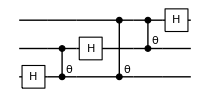

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Keys@dev
```

{DeviceType,DeviceDescription,NumAccessibleQubits,NumTotalQubits,Aliases,Gates,DurationSymbol,Qubits}

```mathematica
conf=DefaultConfig[dev,unitary];
```

```mathematica
HPsummary@conf
```

{ansatzspace→{0,1,2},connectivity→-Graphics-,cost→fidelity,dθ→0.01,fixansatz→{},fixansatzparams→<||>,gateset→<|1→{Rx_#1[θ]&,Ry_#1[θ]&,Rz_#1[θ]&},2→{C_#1[Rx_#2[θ]]&,C_#1[Ry_#2[θ]]&,C_#1[Rz_#2[θ]]&}|>,gradstep→0.01,gradstepmultiply→2,greedflat→0.01,greediness→5,greedinessinit→5,groundstate→0,iterconverge→60,maxbfiter→20,maxcyclefails→3,maxgreediter→200,methode→NG,metignore→1/1000,ngatesinit→24,nqancilla→3,nqmain→3,nqubit→6,parallel→Automatic,perfectingflat→1/1000000,pruningerror→0.1,qancilla→{3,4,5},qmain→{0,1,2},speedupfirst→True,swapfabricdepth→0,usecorr→True,weightgate→{1→0.5,2→0.5},αtikhonov→1/1000,ϵfin→1/1000000,θignore→1/1000,θinitrange→0.1,ρinitu→0,ψinit→1}

```mathematica
CircuitSynthesisCJ[conf]
```

$Aborted